```mathematica
Clear["Global`*"]
```

으아 하기 싫다

```mathematica
T2K100=Import["/Users/WHR/Desktop/work_while_in_cali/T_and_pi/2000_100_T.txt","Table"];
pi2K100=Import["/Users/WHR/Desktop/work_while_in_cali/T_and_pi/2000_100_pi.txt","List"];
(*Drop the last element for plotting / last values are weirdly high / probably due to boundary condition, and we'll fix it later*)
(*Also want to normalize such that min of these functions are all 0 and max of these functions are all 1, using Rescale function in Mathematica*)

h2K100=Import["/Users/WHR/Desktop/work_while_in_cali/T_and_pi/2000_100_h.txt","List"];
h2K100=Drop[h2K100,-1];
h2K100=Rescale[h2K100];
v2K100=Import["/Users/WHR/Desktop/work_while_in_cali/T_and_pi/2000_100_v.txt","List"];
v2K100=Drop[v2K100,-1];
v2K100=Rescale[v2K100];
Nbin=5;
```

```mathematica
refSORT=SortBy[Transpose[{Range[Length[h2K100]],h2K100}],Last];
XvsXH=Transpose[{Range[Length[h2K100]],refSORT[[All,1]]}];
```

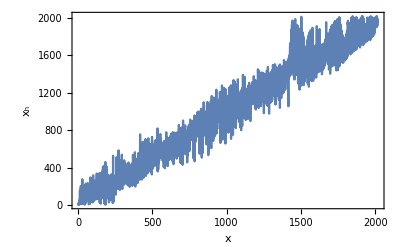

```mathematica
ListLinePlot[XvsXH,PlotRange->All,Frame->True,FrameLabel->{{Style["x_h",18,Black],None},{Style["x",18,Black],None}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{{{18,Black},None},{{18,Black},None}},Axes->False]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/x_to_xh.txt",XvsXH,"Table"];
```

```mathematica
(*Let's sort using values of h rather than just the raw index*)
hSORTED=Array[hsort,{Length[h2K100],2}];
For[k=1,k<Length[h2K100]+1,k++,hSORTED[[k,1]]=k]
For[k=1,k<Length[h2K100]+1,k++,hSORTED[[k,2]]=h2K100[[refSORT[[k,1]]]](*refSORT[[k,2]]*)]
vSORTED=Array[vsort,{Length[v2K100],2}];
For[k=1,k<Length[v2K100]+1,k++,vSORTED[[k,1]]=k]
For[k=1,k<Length[v2K100]+1,k++,vSORTED[[k,2]]=v2K100[[refSORT[[k,1]]]]]
piSORTED=Array[pisort,{Length[pi2K100]-1,2}];
For[k=1,k<Length[pi2K100],k++,piSORTED[[k,1]]=k]
For[k=1,k<Length[pi2K100],k++,piSORTED[[k,2]]=pi2K100[[refSORT[[k,1]]]]]
(*π*v unsorted vs sorted*)
pivSORTED=Array[pivsort,{Length[v2K100],2}];
For[k=1,k<Length[v2K100]+1,k++,pivSORTED[[k,1]]=k]
For[k=1,k<Length[v2K100]+1,k++,pivSORTED[[k,2]]=piSORTED[[k,2]]*vSORTED[[k,2]]]
```

# Binning Strategy s (π*v uniform)

```mathematica
pivSORTEDintegral=Array[pivsortint,{Length[v2K100],2}];
For[k=1,k<Length[v2K100]+1,k++,pivSORTEDintegral[[k,1]]=k]
For[k=1,k<Length[v2K100]+1,k++,pivSORTEDintegral[[k,2]]=Sum[pivSORTED[[l,2]],{l,1,k}]]
```

```mathematica
dpiv=Max[pivSORTEDintegral[[All,2]]]/Nbin;
boundaryS=Array[bndS,Nbin];
For[k=1,k<Nbin+1,k++,
For[l=1,l<Length[v2K100]+1,l++,
If[(k-1)*dpiv<pivSORTEDintegral[[l,2]]&&pivSORTEDintegral[[l,2]]<=k*dpiv,boundaryS[[k]]=l,None]
]
]
boundaryS
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_s.txt",boundaryS,"List"];
```

# Binning Strategy v (π*v k-means)

```mathematica
array=FindClusters[pivSORTEDintegral,Nbin,Method->"KMeans"];
boundaryV=Array[bndV,Nbin];
For[l=1,l<Nbin+1,l++,boundaryV[[l]]=Sum[Length[array[[i]]],{i,1,l}]]
boundaryV
Clear[array];
```

{492,1050,1601,1927,2019}

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_v.txt",boundaryV,"List"];
```

# Binning Strategy p (h uniform)

```mathematica
dh=Max[hSORTED[[All,2]]]/Nbin;
boundaryP=Array[bndP,Nbin];
For[k=1,k<Nbin+1,k++,
For[l=1,l<Length[v2K100]+1,l++,
If[(k-1)*dh<hSORTED[[l,2]]&&hSORTED[[l,2]]<=k*dh,boundaryP[[k]]=l,None]
]
]
boundaryP
```

{651,795,852,992,2019}

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_p.txt",boundaryP,"List"];
```

# Binning Strategy t (h k-means)

```mathematica
array=FindClusters[hSORTED,Nbin,Method->"KMeans"];
boundaryT=Array[bndT,Nbin];
For[l=1,l<Nbin+1,l++,boundaryT[[l]]=Sum[Length[array[[i]]],{i,1,l}]]
boundaryT
Clear[array];
```

{489,811,1099,1559,2019}

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_t.txt",boundaryT,"List"];
```

# Allocation Strategy U (Uniform)

Since it’s uniform (same number of trajectories assigned to each bin), it’s trivial

# Allocation Strategy W (Via Weight / Steady State)

## Binning S

```mathematica
binSallocW=Array[SandW,Nbin];
binSallocW[[1]]=Sum[piSORTED[[i,2]],{i,1,boundaryS[[1]]}];
For[k=2,k<Nbin+1,k++,binSallocW[[k]]=Sum[piSORTED[[i,2]],{i,boundaryS[[k-1]],boundaryS[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_s_alloc_w.txt",binSallocW,"List"];
```

## Binning V

```mathematica
binVallocW=Array[VandW,Nbin];
binVallocW[[1]]=Sum[piSORTED[[i,2]],{i,1,boundaryV[[1]]}];
For[k=2,k<Nbin+1,k++,binVallocW[[k]]=Sum[piSORTED[[i,2]],{i,boundaryV[[k-1]],boundaryV[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_v_alloc_w.txt",binVallocW,"List"];
```

## Binning P

```mathematica
binPallocW=Array[PandW,Nbin];
binPallocW[[1]]=Sum[piSORTED[[i,2]],{i,1,boundaryP[[1]]}];
For[k=2,k<Nbin+1,k++,binPallocW[[k]]=Sum[piSORTED[[i,2]],{i,boundaryP[[k-1]],boundaryP[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_p_alloc_w.txt",binPallocW,"List"];
```

## Binning T

```mathematica
binTallocW=Array[TandW,Nbin];
binTallocW[[1]]=Sum[piSORTED[[i,2]],{i,1,boundaryT[[1]]}];
For[k=2,k<Nbin+1,k++,binTallocW[[k]]=Sum[piSORTED[[i,2]],{i,boundaryT[[k-1]],boundaryT[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_t_alloc_w.txt",binTallocW,"List"];
```

# Allocation Strategy H (Via Weight * Abs[h])

## Binning S

```mathematica
binSallocH=Array[SandH,Nbin];
binSallocH[[1]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,1,boundaryS[[1]]}];
For[k=2,k<Nbin+1,k++,binSallocH[[k]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,boundaryS[[k-1]],boundaryS[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_s_alloc_h.txt",binSallocH,"List"];
```

## Binning V

```mathematica
binVallocH=Array[VandH,Nbin];
binVallocH[[1]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,1,boundaryV[[1]]}];
For[k=2,k<Nbin+1,k++,binVallocH[[k]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,boundaryV[[k-1]],boundaryV[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_v_alloc_h.txt",binVallocH,"List"];
```

## Binning P

```mathematica
binPallocH=Array[PandH,Nbin];
binPallocH[[1]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,1,boundaryP[[1]]}];
For[k=2,k<Nbin+1,k++,binPallocH[[k]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,boundaryP[[k-1]],boundaryP[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_p_alloc_h.txt",binPallocH,"List"];
```

## Binning T

```mathematica
binTallocH=Array[TandH,Nbin];
binTallocH[[1]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,1,boundaryT[[1]]}];
For[k=2,k<Nbin+1,k++,binTallocH[[k]]=Sum[piSORTED[[i,2]]*Abs[hSORTED[[i,2]]],{i,boundaryT[[k-1]],boundaryT[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_t_alloc_h.txt",binTallocH,"List"];
```

# Allocation Strategy V (Via π * v)

## Binning S

```mathematica
binSallocV=Array[SandV,Nbin];
binSallocV[[1]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,1,boundaryS[[1]]}];
For[k=2,k<Nbin+1,k++,binSallocV[[k]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,boundaryS[[k-1]],boundaryS[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_s_alloc_v.txt",binSallocV,"List"];
```

## Binning V

```mathematica
binVallocV=Array[VandV,Nbin];
binVallocV[[1]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,1,boundaryV[[1]]}];
For[k=2,k<Nbin+1,k++,binVallocV[[k]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,boundaryV[[k-1]],boundaryV[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_v_alloc_v.txt",binVallocV,"List"];
```

## Binning P

```mathematica
binPallocV=Array[PandV,Nbin];
binPallocV[[1]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,1,boundaryP[[1]]}];
For[k=2,k<Nbin+1,k++,binPallocV[[k]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,boundaryP[[k-1]],boundaryP[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_p_alloc_v.txt",binPallocV,"List"];
```

## Binning T

```mathematica
binTallocV=Array[TandV,Nbin];
binTallocV[[1]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,1,boundaryT[[1]]}];
For[k=2,k<Nbin+1,k++,binTallocV[[k]]=Sum[piSORTED[[i,2]]*vSORTED[[i,2]],{i,boundaryT[[k-1]],boundaryT[[k]]}]]
```

```mathematica
Export["/Users/WHR/Desktop/work_while_in_cali/mod_WE/runs/strategies/bin_t_alloc_v.txt",binTallocV,"List"];
```